# The Duffing Equation with Mathematica

Dr. Gustavo A. Pérez M.
Honduras National Academy of Sciences
gus@pepper.org

### Perception is everything

Abstract :
We use Mathematica to obtain the analytical and numerical solutions of Duffing equation.

## Introduction

We consider as Duffing problem the differential equation:
u''+u+ϵ u^3=0, as initial conditions, we take u(0)=x_0 and u'(0)=v_0.
The solution u of our problem is a function of the independent variable t and the parameter ϵ that is a dimensionless quantity, and its a measure of the strength of the non linearity. Then, an exact solution has a frequency ω that is a function of ϵ, the non linearity.
Mathematica solves numerically the Duffing problem.

```mathematica
eqdu=u''[t]+ u[t]+ϵ u[t]^3==0
```

u[t]+ϵ u[t]^3+u''[t]==0

```mathematica
eqdv=v''[t]+ v[t]+ϵ v[t]^3==0
```

v[t]+ϵ v[t]^3+v''[t]==0

We write the same equation two times in order to solve one for the amplitude eqdu and the other for the velocity eqdv with diferent initial conditions.

## The potential energy and the solutions

The Duffing problem, as defined, is periodic and conservative, we keep the parameter ϵ in the necessary range as to satisfy these conditions.
Let define the potential energy:

```mathematica
F[u_,ϵ_]:=1/2 u^2+ 1/4 ϵ u^4
```

```mathematica
Plot3D[F[u,ϵ],{u,-1.5,1.5},{ϵ,-1,1}]
```

-Graphics3D-

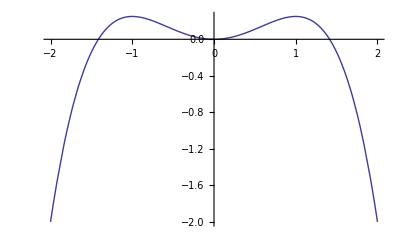

```mathematica
Plot[F[u,-1],{u,-2,2}]
```

The energy equation

```mathematica
eqce=1/2 v^2+F[u,ϵ]==h
```

u^2/2+v^2/2+(u^4 ϵ)/4==h

The relation between amplitude and velocity

```mathematica
eqa=1/2 Subscript[v, 0]^2==Subscript[x, 0]^2/2+(ϵ Subscript[x, 0]^4)/4
```

v_0^2/2==x_0^2/2+(ϵ x_0^4)/4

```mathematica
Solve[eqa,Subscript[x, 0]]
```

{{x_0→-√(-1/ϵ-(√(1+2 ϵ v_0^2))/ϵ)},{x_0→√(-1/ϵ-(√(1+2 ϵ v_0^2))/ϵ)},{x_0→-√(-1/ϵ+(√(1+2 ϵ v_0^2))/ϵ)},{x_0→√(-1/ϵ+(√(1+2 ϵ v_0^2))/ϵ)}}

Where the only valid solution is x_0→√(-1/ϵ+(√(1+2 ϵ v_0^2))/ϵ)

Whenever ϵ>0 the velocity is zero in two points and the trajectory is closed and periodic. Whenever ϵ<0 the trajectory could be closed and periodic for some values of h or could be unlimited for values of h beyond the maxima of the potential.
When the trajectory is closed and periodic the initial conditions are in some way limited by the energy conservation and a problem of initial velocity is equivalent after some time to a initial amplitude problem.

The equation of energy conservation eqce could be written as:
1/2 v^2=h-1/2 u^2- 1/4 ϵ u^4=h-F(u,ϵ)

```mathematica
eqe=1/2 v^2==h-1/2 u^2- 1/4 ϵ u^4
```

v^2/2==h-u^2/2-(u^4 ϵ)/4

```mathematica
Solve[eqe,v]
```

{{v→-√2 √(h-u^2/2-(u^4 ϵ)/4)},{v→√2 √(h-u^2/2-(u^4 ϵ)/4)}}

If we do u'=du/dt=v and integrate:
t=±∫_x_0^u 1/(√(2 h-u^2-1/2 ϵ u^4))ⅆu
Introducing the amplitude in the energy conservation
h=1/2x_0^2+1/4ϵ x_0^4
and making the transformation
u=-x_0Cos(θ)

This takes some minutes

eq1=t1==1/(√(1+ϵ x_0^2))Integrate[1/(√(1-m Sin[θ]^2)),{θ,θ1,θ2},Assumptions→m>0&&m<1&&θ1<θ2]

t1==(-EllipticF[θ1,m]+EllipticF[θ2,m])/(√(1+ϵ x_0^2))

```mathematica
eq1=t1==(-EllipticF[θ1,m]+EllipticF[θ2,m])/(√(1+a))
```

t1==(-EllipticF[θ1,m]+EllipticF[θ2,m])/(√(1+a))

This is our principal equation and gives the analytical solution to the Duffing problem other name is the first integral of movement.
The value of m is:

m=(ϵ x_0^2)/(2 (1+ ϵ x_0^2))

## Analytical solution for a initial amplitude

In our transformation a initial amplitude and zero initial velocity is characterized by θ1→0.

```mathematica
S1=Solve[eq1/.θ1->0,θ2]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{θ2→JacobiAmplitude[√(1+a) t1,m]}}

In this case the solution is:
u[t]=-x_0JacobiCn[t1 √(1+ϵ x_0^2),m] and making  a=ϵ x_0^2.

```mathematica
ua[t_]=-Subscript[x, 0]JacobiCN[t √(1+a),m]
```

-JacobiCN[√(1+a) t,m] x_0

## Analytical solution for a initial velocity

In this case we find the amplitude equivalent for the velocity

x_0=√(-1/ϵ+(√(1+2 ϵ v_0^2))/ϵ)

This solution is characterized by θ1→π/2

```mathematica
S2=Solve[eq1/.θ1->π/2,θ2]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{θ2→JacobiAmplitude[√(1+a) t1+EllipticK[m],m]}}

The solution is

```mathematica
uv[t_]=-Subscript[x, 0]JacobiCN[EllipticK[a/(2 (1+a))]+t √(1+a),a/(2 (1+a))]
```

√(1-a/(2 (1+a))) JacobiSD[√(1+a) t,a/(2 (1+a))] x_0

```mathematica
uv[t_]=JacobiSD[t √(1+ϵ (-1/ϵ+(√(1+2 ϵ Subscript[v, 0]^2))/ϵ)),(ϵ (-1/ϵ+(√(1+2 ϵ Subscript[v, 0]^2))/ϵ))/(2 (1+ϵ (-1/ϵ+(√(1+2 ϵ Subscript[v, 0]^2))/ϵ)))] √(-1/ϵ+(√(1+2 ϵ Subscript[v, 0]^2))/ϵ) √(1-(ϵ (-1/ϵ+(√(1+2 ϵ Subscript[v, 0]^2))/ϵ))/(2 (1+ϵ (-1/ϵ+(√(1+2 ϵ Subscript[v, 0]^2))/ϵ))))
```

JacobiSD[t √(1+ϵ (-1/ϵ+(√(1+2 ϵ v_0^2))/ϵ)),(ϵ (-1/ϵ+(√(1+2 ϵ v_0^2))/ϵ))/(2 (1+ϵ (-1/ϵ+(√(1+2 ϵ v_0^2))/ϵ)))] √(-1/ϵ+(√(1+2 ϵ v_0^2))/ϵ) √(1-(ϵ (-1/ϵ+(√(1+2 ϵ v_0^2))/ϵ))/(2 (1+ϵ (-1/ϵ+(√(1+2 ϵ v_0^2))/ϵ))))

## The Period

Since the time needed to move from u=-x_0 to u=x_0 is one half the period then

```mathematica
T=2/(√(1+ϵ Subscript[x, 0]^2))Integrate[1/(√(1-m Sin[θ]^2)),{θ,0,π},Assumptions->m<1]
```

(2 (EllipticK[m]+EllipticK[m/(-1+m)]/(√(1-m))))/(√(1+ϵ x_0^2))

```mathematica
Ta[m_,a_]=T/.ϵ Subscript[x, 0]^2->a
```

(2 (EllipticK[m]+EllipticK[m/(-1+m)]/(√(1-m))))/(√(1+a))

## Numerical Solutions

Mathematica solves the numerical Duffing problem, here we obtain the numerical solutions and its comparison with the analytical results.

```mathematica
Subscript[x, 0]=1;ϵ=1;Subscript[v, 0]=1;
```

```mathematica
a=ϵ Subscript[x, 0]^2;
```

This is the numerical solution for x_0=1

```mathematica
m=(ϵ Subscript[x, 0]^2)/(2 (1+ ϵ Subscript[x, 0]^2))
```

1/4

```mathematica
sol1=NDSolve[{eqdu/.ϵ->1,u[0]==-1,u'[0]==0},u,{t,0,5}]
```

{{u→InterpolatingFunction[{{0.,5.}},<>]}}

The form of the solution for the amplitude x_0 is:

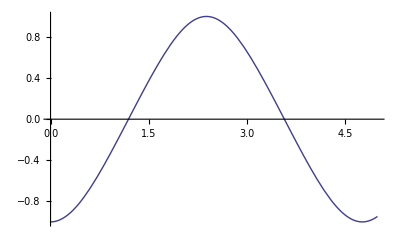

```mathematica
Plot[ua[t],{t,0,5}]
```

Note here that even if the solution is a Cosine the frequency is a function of the non lineality ϵ.

Comparison with the analytical solution

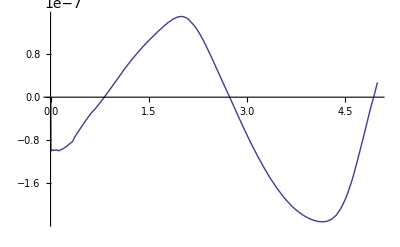

```mathematica
Plot[ua[t]-Evaluate[u[t]/.sol1],{t,0,5}]
```

The numerical solution for v_0

```mathematica
Subscript[x, 0]=√(-1/ϵ+(√(1+2 ϵ Subscript[v, 0]^2))/ϵ)
```

√(-1+√3)

```mathematica
m=(ϵ Subscript[x, 0]^2)/(2 (1+ ϵ Subscript[x, 0]^2))
```

(-1+√3)/(2 √3)

```mathematica
sol2=NDSolve[{eqdv/.ϵ->1,v[0]==0,v'[0]==1},v,{t,0,5}]
```

{{v→InterpolatingFunction[{{0.,5.}},<>]}}

The form of the solution for v_0 is:

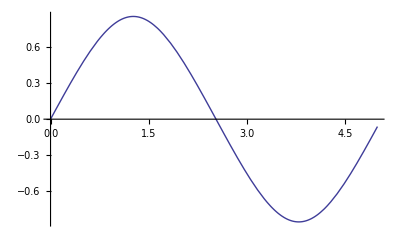

```mathematica
Plot[uv[t],{t,0,5}]
```

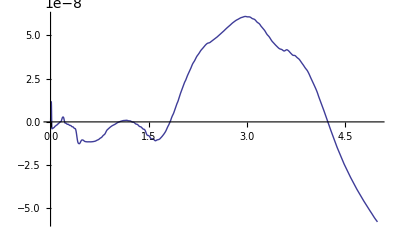

```mathematica
Plot[uv[t]-Evaluate[v[t]/.sol2],{t,0,5}]
```

## Values of the Exact Period

The values of the exact period could be tabulated as a function of m and a the non linearity.

```mathematica
mt={0,0.02,0.04,0.06,0.08,0.1}
```

{0,0.02,0.04,0.06,0.08,0.1}

```mathematica
at={0,0.042,0.087,0.136,0.190,0.25}
```

{0,0.042,0.087,0.136,0.19,0.25}

```mathematica
Ta[mt,at]
```

{2 π,6.18638,6.08816,5.98663,5.88047,5.76885}

```mathematica
Grid[{mt,at,Ta[mt,at]},Frame->All]
```

0 | 0.02 | 0.04 | 0.06 | 0.08 | 0.1
0 | 0.042 | 0.087 | 0.136 | 0.19 | 0.25
2 π | 6.18638 | 6.08816 | 5.98663 | 5.88047 | 5.76885

This proves that the period and frequency depend on the non linearity.

## Conclusions

We use Mathematica to find the analytical solutions of the Duffing problem without friction. With the numerical capabilities of Mathematica,  we check our solutions. 

The Jacobi Elliptic functions  result of the variable transformation and the solution of the first integral for θ2,  that is a Jacobi Amplitude.

Mathematica could be used to bring the students of the level of the Nayfeh book to use the Jacobi Elliptic functions without effort.

## References

Nayfeh, Ali Hasan. Introduction to Perturbation Techniques. John Wiley & Sons 1993. Page 113 to 118.
Shivamoggi, Bhimsen K. Perturbation Methods for Differential Equations. Birkhausser Boston 2003. Page 25 to 28.
Introduction to the Jacobi elliptic functions. http://functions.wolfram.com/EllipticFunctions/JacobiNC/introductions/JacobiPQs/ShowAll.html